## Calc3-Mathematica-Rechnungen

Dieses Notebook sammelt die relevanten Differentialgleichungs-Rechnungen zu Calc3 (Master).

```mathematica
ODE= f'[r] + (n+1)/r *f[r] == 1/MStar * 2 r ρ[r] / (n+2)
```

((1+n) f[r])/r+f'[r]==(2 r ρ[r])/(MStar (2+n))

### Rizzo-Rechnungen

Rizzo verwendet Nicolinis NonCommutative-Dichte ρ (Exp-Funktion). Ich rechne hier Rizzos Ergebnis nach.

```mathematica
Rizzo = ODE /. { ρ[r] -> M/((4Pi θ)^((n+3)/2)) * Exp[-r^2/(4θ)]}
```

((1+n) f[r])/r+f'[r]==(2^(-2-n) ⅇ^(-r^2/(4 θ)) M π^(1/2 (-3-n)) r θ^(1/2 (-3-n)))/(MStar (2+n))

```mathematica
DSolve[Rizzo,{f[r]},{r}] // Simplify
```

{{f[r]→r^(-1-n) C[1]-(M π^(-3/2-n/2) (r^2/θ)^(-1/2-n/2) θ^(-1/2-n/2) Gamma[(3+n)/2,r^2/(4 θ)])/(MStar (2+n))}}

```mathematica
fRizzo[r_] = (M π^(-3/2-n/2) (r^2/θ)^(-1/2-n/2) θ^(-1/2-n/2) Gamma[(3+n)/2,r^2/(4 θ)])/(MStar (2+n));
```

```mathematica
(* Freie Parameter bei Rizzo: M, MStar, n, θ *)
(* Unterstrich mit Esc_Esc *)
RH Rizzo = D[1- fRizzo[r], r] // FullSimplify
```

-((2^(1-n) ⅇ^(-r^2/(4 θ)) M π^(-3/2-n/2) r^3 θ^(-3/2-n/2))/(MStar (2+n))-8 (1+n) r^-n C[1]+(2^-n M (1+n) π^(-3/2-n/2) r^3 θ^(-3/2-n/2) ExpIntegralE[-1/2-n/2,r^2/(4 θ)])/(MStar (2+n)))/(8 r^2)

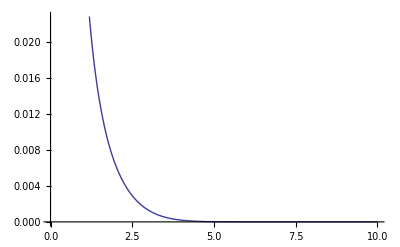

```mathematica
Plot[ fRizzo[r]/.{MStar -> 1, M -> 1,θ -> 1, n -> 1 }, {r, 0, 10}]
```

```mathematica
(* Vgl Rizzopaper Figure 7, Seite 13. Mit meinen Annahmen für M, ... sagen die Plots gar nichts aus *)
```

### Generische Holographie-Lösung

In diesem Abschnitt untersuche ich die allgemeinste Form von ρ mit Ableitung von h(r) drin. Ich denke, das ist vermutlich mein Job, als Analogon zu Rizzo. Diskutiere ich am 06.12. mit PN.

```mathematica
Hgener = ODE /. { ρ[r] ->M/Ω D[h[r], r]}
```

((1+n) f[r])/r+f'[r]==(2 M r h'[r])/(MStar (2+n) Ω)

```mathematica
DSolve[Hgener,{f[r]},{r}]
```

{{f[r]→r^(-1-n) C[1]+r^(-1-n) ∫_1^r (2 M K[1]^(2+n) h'[K[1]])/(MStar (2+n) Ω)ⅆK[1]}}

```mathematica
g[x_] = D[x^2/(x^2 + L^2),x]
```

-(2 x^3)/((L^2+x^2)^2)+(2 x)/(L^2+x^2)

```mathematica
(* Interessanterweise setzt das folgende Integral scharfe Bedingungen
  an r in Bezug auf L, wie z.B. 0 < L < r *)
```

```mathematica
Assuming[Im[r]==0 ∧ r≥ L ∧L≥ 0∧Im[L] == 0, r^(-1-n) C[1]+r^(-1-n) ∫_L^r (2 M x^(2+n) g[x])/(MStar (2+n) Ω)ⅆx ]
```

ConditionalExpression[r^(-1-n) C[1]+(L^2 M r^(-1-n) (2 n (L^(2+n)+L^n r^2-2 r^(2+n))+4 (2+n) r^n (L^2+r^2) Hypergeometric2F1[1,-n/2,1-n/2,-L^2/r^2]+L^n n (2+n) (L^2+r^2) PolyGamma[0,1/2-n/4]-L^n n (2+n) (L^2+r^2) PolyGamma[0,-n/4]))/(2 n (L^2+r^2) (2 MStar Ω+MStar n Ω)),r>0&&0<L<r]

```mathematica
(* Komplett ohne Assuming kommt folgender Term raus, die ConditionalExpression-Bedingungen nahm ich mal alle als Gegeben an: *)
```

```mathematica
r^(-1-n) C[1]+1/(MStar (2+n) Ω)4 L^2 M r^(-1-n) (-(-L^2+(1+L^2) Hypergeometric2F1[1,(2+n)/2,(4+n)/2,-1/L^2])/(2 L^2 (1+L^2))+(r^(2+n) (-L^2+(L^2+r^2) Hypergeometric2F1[1,(2+n)/2,(4+n)/2,-r^2/L^2]))/(2 L^2 (L^2+r^2))) // FullSimplify
```

```mathematica
(* Dann ist das hier mein f(r) in dieser Theorie *)
```

```mathematica
fh[r_] = r^(-1-n) (1/(MStar (2+n) Ω)2 M (L^2 (1/(1+L^2)-r^(2+n)/(L^2+r^2))-Hypergeometric2F1[1,(2+n)/2,(4+n)/2,-1/L^2]+r^(2+n) Hypergeometric2F1[1,(2+n)/2,(4+n)/2,-r^2/L^2]))/.{MStar->1,M->1,Ω->1,L-> 1}
```

1/(2+n)2 r^(-1-n) (1/2-r^(2+n)/(1+r^2)+r^(2+n) Hypergeometric2F1[1,(2+n)/2,(4+n)/2,-r^2]+1/4 (2+n) (PolyGamma[0,1/2+n/4]-PolyGamma[0,1+n/4]))

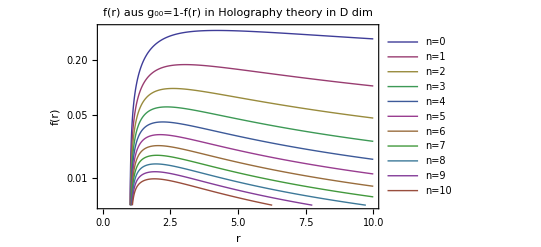

```mathematica
LogPlot[
	Evaluate[Table[fh[x],{n,0,10}]] ,{x,0,10},
	PlotRange->{0.005, 0.45}, 
	PlotLegends->Placed[Table["n="<>ToString[n],{n,0,10}], Below],
	Frame-> True,
	FrameLabel -> {r, "f(r)"},
	PlotLabel -> "f(r) aus g_00=1-f(r) in Holography theory in D dim"]
```

### Holographie-Lösung mit h_α(r)

Das sollte ich auch irgendwie untersuchen:

```mathematica
DAlphi = ODE /. { ρ[r] -> r^k/(r^α + (r0)^α / 2)^(k/α)}
```

((1+n) f[r])/r+f'[r]==(2 r^(1+k) (r^α+r0^α/2)^(-k/α))/(MStar (2+n))

```mathematica
DNAlphi = DAlphi /. {k-> 3+n}
```

((1+n) f[r])/r+f'[r]==(2 r^(4+n) (r^α+r0^α/2)^(-(3+n)/α))/(MStar (2+n))

```mathematica
DSolve[DNAlphi,{f[r]},{r}]
```

{{f[r]→r^(-1-n) C[1]+1/(MStar (2+n) (3+n))r^(5+n) (1+2 r^α r0^-α)^((3+n)/α) (r^α+r0^α/2)^(-(3+n)/α) Hypergeometric2F1[(3+n)/α,(2 (3+n))/α,(6+2 n+α)/α,-2 r^α r0^-α]}}

```mathematica
r^(-1-n) C[1]+1/(MStar (2+n) (3+n))r^(5+n) (1+2 r^α r0^-α)^((3+n)/α) (r^α+r0^α/2)^(-(3+n)/α) Hypergeometric2F1[(3+n)/α,(2 (3+n))/α,(6+2 n+α)/α,-2 r^α r0^-α] // FullSimplify
```

```mathematica
r^(-1-n) C[1]+(r^(5+n) (1+2 r^α r0^-α) (r^α+r0^α/2)^(-(3+n)/α) Hypergeometric2F1[1,(3+n+α)/α,(6+2 n+α)/α,-2 r^α r0^-α])/(MStar (2+n) (3+n))/. {n-> 0}
```

C[1]/r+(r^5 (1+2 r^α r0^-α) (r^α+r0^α/2)^(-3/α) Hypergeometric2F1[1,(3+α)/α,(6+α)/α,-2 r^α r0^-α])/(6 MStar)